## 3.029 Spring 2022 Lecture 20 - 04/13/2022

## Statistical Mechanics II

## Ensembles Reminder

Last lecture, we introduced the concept of statistical ensembles, and how we can use them to extract meaningful thermodynamic quantities

We outlined the following general steps

Decide the relevant thermodynamic potential

This is often set by “experimental” conditions.
“Experimental” here might refer to conditions you can control in your numerical simulation (e.g. the number and total energy of the particles)

The natural variables of your thermodynamic potential define your statistical ensemble

Entropy  			→	NVE ensemble, aka Micro-canonical ensemble

Helmholtz free energy 	→	NVT ensemble, aka Canonical ensemble

Grand potential 		→	μVT ensemble, aka Grand-canonical ensemble

Compute the partition function for the statistical ensemble

NVE ensemble		→	“Degeneracy”,

NVE ensemble		→	“Partition Function”,

μVT ensemble		→	“Grand Partition Function”,

Calculate the relevant thermodynamic potential using the partition function

“Degeneracy”			→	Entropy,

“Partition Function”		→	Helmholtz free energy,

“Grand Partition Function”	→	Grand potential,

Use the differential form of the thermodynamic potential to obtain all other thermodynamic quantities

Entropy,			 		→	Inverse temperature, internal energy, etc..

Helmholtz free energy,				→	Entropy, internal energy, etc..

Grand potential,				→	Chemical potential, internal energy, etc..

## Lennard Jones Dimer

In the staircase example we saw last time, the different microstates all had discrete energy levels

This is actually rather reminiscent of quantum-mechanical systems, which you will be study next semester

Let’s investigate a system with continuous energy levels, using our favourite interatomic potential

```mathematica
lennardJonesPotentialNonDimensional[ρ_]=1/ρ^12-2/ρ^6;
lennardJonesForce[ρ_]=-lennardJonesPotentialNonDimensional'[ρ];
```

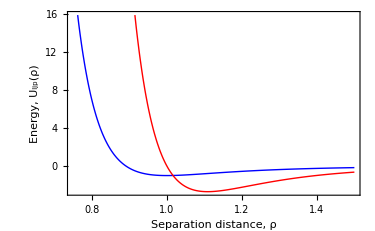

```mathematica
Plot[{lennardJonesPotentialNonDimensional[ρ],lennardJonesForce[ρ]},{ρ,3/4,3/2},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"Separation distance, ρ","Energy, U_ljp(ρ)"},BaseStyle->16,ImageSize->375]
```

We want to analyze the possible configurations a Lennard-Jones dimer can take in a Microcanonical ensemble

I.e. we need to evolve the system at constant energy

To do this, we will use the symplectic integration scheme we introduced in L13

```mathematica
parametricNDSolveValue=ParametricNDSolveValue[{
p'[t]==lennardJonesForce[q[t]], 
q'[t] == p[t],
 p[0] == 0,
q[0]==q0,
count[0]==0,
WhenEvent[p[t]==0,{count[t]->count[t]+1,If[count[t]>= 2,"StopIntegration"]}]
},{q,p},{t,0,100},q0,DiscreteVariables->{count},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->4,"PositionVariables"->{q[t]}}]
```

ParametricFunction[<>]

Notes:

We used an auxiliary “count” variable to count the zero-momentum crossings and stop the integration scheme

We used ParametricNDSolveValue to vary the initial position of the particle

We can know plot the dimer’s position, q[t] vs its momentum, p[t]

I.e. the phase - space

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
phaseVariables[initialPosition_]:=Block[{psol,qsol,time},
{qsol,psol}=parametricNDSolveValue[initialPosition];
time=InterpolatingFunctionDomain[psol][[1,-1]];
{{psol,qsol},time}
]
```

If we only start at initial displacements ρ_0>2^(-1/6), we’re guaranteed to have a “bound state” which will oscillate around the minimum

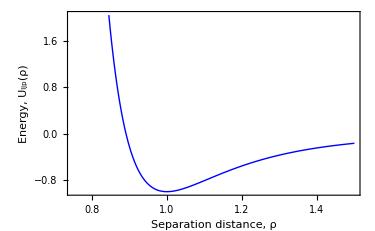

```mathematica
Plot[lennardJonesPotentialNonDimensional[ρ],{ρ,3/4,3/2},PlotStyle->Directive[Blue,Thick],Frame->True,FrameStyle->Directive[Black,Thick],GridLines->{{2^(-1/6)},None},FrameLabel->{"Separation distance, ρ","Energy, U_ljp(ρ)"},BaseStyle->16,ImageSize->375]
```

Indeed, if we plot the momentum vs the position for a range of initial displacements

we obtain closed orbits

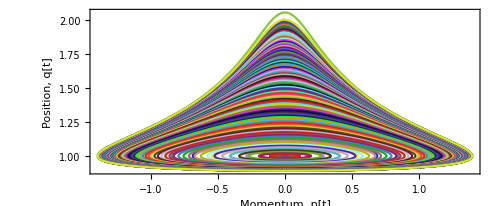

```mathematica
plots =With[{solutions = phaseVariables/@Subdivide[2^(-1/6)+0.001,2,100]},
Show[
ParametricPlot[Through[First[#][t]],{t,0,Last[#]},PlotStyle->RandomColor[]]&/@solutions
,Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->Automatic,FrameLabel->{"Momentum, p[t]","Position, q[t]"},LabelStyle->Directive[14,Black],ImageSize->500]
]
```

Let’s ensure our simulations were indeed conserving energy

Seems like our error is at-most 1%, and often much smaller - so this is fine

```mathematica
Manipulate[
With[{sol=phaseVariables[q0],ϵ0=lennardJonesPotentialNonDimensional[q0]},
Plot[(ϵ0-(lennardJonesPotentialNonDimensional[#1[[2]][t]]+(#1[[1]][t])^2/2))/ϵ0 100,{t,0,#2},GridLines->{None,{ϵ0}},GridLinesStyle->Directive[Gray,Dashed],PlotStyle->Red,Frame->True,PlotRange->All]&@@sol
],{{q0,1.4},2^(-1/6)+0.001,2},Paneled->False]
```

Since we’re indeed evolving at constant-energy, each closed loop above is a microcanonical ensemble

I.e. each point on a closed loop, is a particular (continuous) microstate of the microcanonical ensemble with that particular energy

In L19, we mentioned that the degeneracy of the microcanonical ensemble can also be given by the “surface area” of the constant-energy surface

Since our phase-space is only 2D in this case, the degeneracy is given by the arclength of our trajectories

```mathematica
?ArcLength
```

```mathematica
ArcLength[{p[t],q[t]},{t,0,t0}]
```

Integrate[√(p'[t]^2+q'[t]^2),{t,0,t0},Assumptions→0<t0]

Note however we need to rescale this such that the zero arc-length point, i.e. at ρ=1, has the ground state degeneracy of 1

As such, we’ll add one to our arc-length values

```mathematica
energyAndDegeneracy[initialPosition_]:=With[{sol=phaseVariables[initialPosition]},
{lennardJonesPotentialNonDimensional[initialPosition],1+Quiet@ArcLength[Through[#1[t]],{t,0,#2}]&@@sol}]
```

```mathematica
lennardJonesDegeneracy=Interpolation[energyAndDegeneracy/@Subdivide[2^(-1/6)+0.001,2,100]]
```

InterpolatingFunction[…]

Let’s plot it!

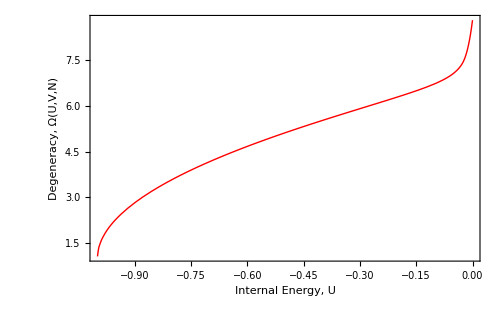

```mathematica
Quiet[Plot[lennardJonesDegeneracy[ϵ],{ϵ,-1,0},Frame->True,LabelStyle->Directive[Black,Thick,16],ImageSize->500,PlotStyle->Directive[Red,Thick],FrameLabel->{"Internal Energy, U","Degeneracy, Ω(U,V,N)"}]]
```

We can know use Boltzmann’s formula to get the entropy

```mathematica
lennardJonesEntropy[ϵ_]=Log[lennardJonesDegeneracy[ϵ]]
```

Log[InterpolatingFunction[…][ϵ]]

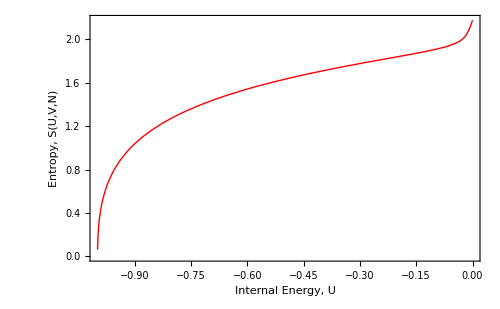

```mathematica
Quiet[Plot[lennardJonesEntropy[ϵ],{ϵ,-1,0},Frame->True,LabelStyle->Directive[Black,Thick,16],ImageSize->500,PlotStyle->Directive[Red,Thick],FrameLabel->{"Internal Energy, U","Entropy, S(U,V,N)"}]]
```

Hmm, this uptick is actually somewhat unexpected/worrying..

## Frenkel Defects

Consider a perfect square lattice (ground state)

```mathematica
groundState[numberOfAtoms_]:=Graphics[{Disk[#,1/(2numberOfAtoms)]&/@Tuples[Subdivide[-1,1,numberOfAtoms-1],2]},PlotRange->(numberOfAtoms+1)/(numberOfAtoms-1){{-1,1},{-1,1}}]
```

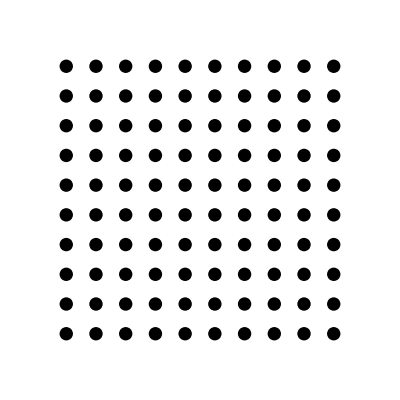

```mathematica
groundState[10]
```

Create Frenkel defects (vacancy - interstitial pair)

The ground state has energy 0, while each Frenkel defect ‘costs’ an energy of ϵ

```mathematica
frenkelDefect[numberOfAtoms_,numberOfDefects_:1]:=With[{gs=Tuples[Subdivide[-1,1,numberOfAtoms-1],2]},
Graphics[{
Disk[#,1/(2numberOfAtoms)]&/@Union[RandomSample[gs,Length[gs]-numberOfDefects]],
Red,Disk[#+{1,1}/(numberOfAtoms-1),1/(2numberOfAtoms)]&/@Union[RandomSample[gs,numberOfDefects]]},
PlotRange->(numberOfAtoms+1)/(numberOfAtoms-1){{-1,1},{-1,1}}]]
```

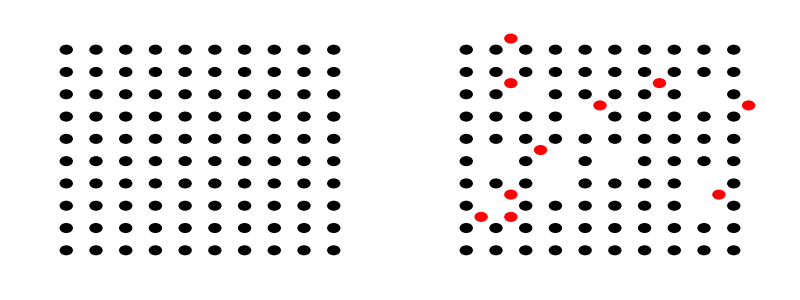

```mathematica
Multicolumn[{groundState[10],frenkelDefect[10,10]},2]
```

Since we can choose the vacancy in one of N positions, and similarly the interstitial in N, the # of different configurations is given by:

Ω(N)=N^2

```mathematica
binomial[n_,k_]:=ExpandAll[(n!)/((n-k)!k!)]
```

```mathematica
binomial[9,1]^2
Table[frenkelDefect[3],5000]//Union//Length
```

81

81

```mathematica
Multicolumn[Table[frenkelDefect[3],5000]//Union,9,Frame->All,Appearance->"Horizontal"]
```

If we allow for m Frenkel defects in a lattice with N atoms, then this would be given by:

Ω(N,m)=(N
m)^2

```mathematica
binomial[9,2]^2
Table[frenkelDefect[3,2],10000]//Union//Length
```

1296

1296

```mathematica
FunctionExpand[binomial[n,m]^2]
```

Gamma[1+n]^2/(Gamma[1+m]^2 Gamma[1-m+n]^2)

### Canonical Partition Function

Since we only have two levels, it’s simple to write the partition function.

```mathematica
partitionFunction["frenkel"][n_,m_,ϵ_][τ_]=Exp[0]+Gamma[1+n]^2/(Gamma[1+m]^2 Gamma[1-m+n]^2)Exp[-m ϵ/τ]
```

1+(ⅇ^(-(m ϵ)/τ) Gamma[1+n]^2)/(Gamma[1+m]^2 Gamma[1-m+n]^2)

Where we’ve used the Gamma function to expand the degeneracy of multiple Frenkel defects.

### Thermodynamic Potentials

We then proceed as usual to recover the free energy, entropy, and internal energy

```mathematica
helmholtzFreeEnergy ["frenkel"][n_,m_,ϵ_][τ_]= FullSimplify[-τ Log[partitionFunction["frenkel"][n,m,ϵ][τ]],Assumptions->{τ,n,ϵ,m}>0]
```

-τ Log[1+(ⅇ^(-(m ϵ)/τ) Gamma[1+n]^2)/(Gamma[1+m]^2 Gamma[1-m+n]^2)]

```mathematica
entropy["frenkel"][n_,m_,ϵ_][τ_]=FullSimplify[-helmholtzFreeEnergy ["frenkel"][n,m,ϵ]'[τ],Assumptions->{τ,n,ϵ,m}>0]
```

(m ϵ Gamma[1+n]^2)/(τ Gamma[1+n]^2+ⅇ^((m ϵ)/τ) τ Gamma[1+m]^2 Gamma[1-m+n]^2)+Log[1+(ⅇ^(-(m ϵ)/τ) Gamma[1+n]^2)/(Gamma[1+m]^2 Gamma[1-m+n]^2)]

```mathematica
internalEnergy["frenkel"][n_,m_,ϵ_][τ_]=FullSimplify[helmholtzFreeEnergy ["frenkel"][n,m,ϵ][τ]+ τ entropy["frenkel"][n,m,ϵ][τ], Assumptions->{τ,n,ϵ,m}>0]
```

(m ϵ Gamma[1+n]^2)/(Gamma[1+n]^2+ⅇ^((m ϵ)/τ) Gamma[1+m]^2 Gamma[1-m+n]^2)

Discontinuities in these functions suggest a phase-transition

```mathematica
Manipulate[Quiet@Plot[(internalEnergy["frenkel"][n,n/ratio,1][τ])/(n/ratio),{τ,0,1},Frame->True,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->Directive[Red,Thick],BaseStyle->18,ImageSize->500],{n,10,1000},{ratio,2,10},Paneled->False]
```

Indeed, in the thermodynamic limit (n → ∞), we get a discontinuity and thus a phase transition at finite temperature.
Let’s find that temperature!

```mathematica
Limit[ratio internalEnergy["frenkel"][n,n/ratio,ϵ][τ]/n,n->∞,Assumptions->{ratio>1,ϵ>0,τ>0}]
```

$Aborted

```mathematica
phaseTransitionTemperature[ϵ_,ratio_]=SolveValues[τ (ϵ-2 τ Log[(-1+ratio)/ratio]+2 a τ Log[(-1+ratio)/ratio]-2 τ Log[ratio])==0,τ[[2,1]]]
```

ϵ/(2 (Log[(-1+a)/a]-a Log[(-1+a)/a]+Log[a]))

```mathematica
Limit[phaseTransitionTemperature[ϵ,a],a->∞]
```

0

## Binary Alloys

## Polymer Chains